```mathematica
FullSimplify[Cos[a(1+ⅈ)]==Cos[a]Cosh[a]-ⅈ Sin[a]Sinh[a]]
```

True

```mathematica
FullSimplify[Sin[a(1+ⅈ)]==Sin[a]Cosh[a]+ⅈ Cos[a]Sinh[a]]
```

True

```mathematica
FullSimplify[1/(1+ⅈ)^3==-(1+ⅈ)/4]
```

True

```mathematica
FullSimplify[(Cos[a]Cosh[a])^2+(Sin[a]Sinh[a])^2==(Cos[2a]+Cosh[2a])/2]
```

True

Q^-1を求めるときに使った (231106)

```mathematica
FullSimplify[Cos[a d]Cosh[a d]Cos[a] Sinh[a]==1/4(Cos[a(d+1)]+Cos[a(d-1)])(Sinh[a(1+d)]+Sinh[a(1-d)])]
```

True

```mathematica
FullSimplify[Cos[a d]Cosh[a d]Sin[a] Cosh[a]==1/4(Sin[a(d+1)]-Sin[a(d-1)])(Cosh[a(1+d)]+Cosh[a(1-d)])]
```

True

```mathematica
FullSimplify[Cos[a d]Cosh[a d]Cos[a] Cosh[a]==1/4(Cos[a(d+1)]+Cos[a(d-1)])(Cosh[a(1+d)]+Cosh[a(1-d)])]
```

True

```mathematica
FullSimplify[Sin[a d]Sinh[a d]Cos[a] Sinh[a]==1/4(Sin[a(d+1)]+Sin[a(d-1)])(Cosh[a(1+d)]-Cosh[a(1-d)])]
```

True

```mathematica
FullSimplify[Sin[a d]Sinh[a d]Sin[a] Cosh[a]==1/4(-Cos[a(d+1)]+Cos[a(d-1)])(Sinh[a(1+d)]-Sinh[a(1-d)])]
```

True

```mathematica
FullSimplify[Sin[a d]Sinh[a d]Sin[a] Sinh[a]==1/4(-Cos[a(d+1)]+Cos[a(d-1)])(Cosh[a(1+d)]-Cosh[a(1-d)])]
```

True

三角関数と双曲線関数のオーダーを知りたい

cos[ξ]

Cos[0.000838 √f]

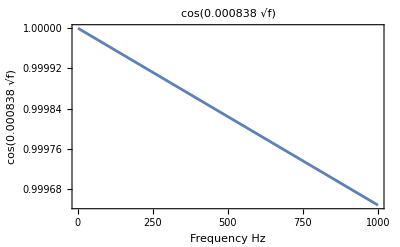

```mathematica
cos=Cos[ξ]/.
{ξ->8.38 10^-4 √f}
(*{ξ->b/2 √(ω/(2χ))}/.
{ω->2π f,χ->4.47,b->2 10^-3};*)
cosg=Plot[cos,{f,1,1000},PlotLabel->cos, Frame->True,FrameLabel->{Frequency(Hz),cos}]
```

sin[ξ]

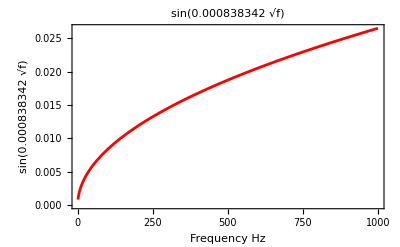

```mathematica
sin=Sin[ξ]/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
sing=Plot[sin,{f,1,1000},PlotLabel->sin,PlotStyle->{Red}, Frame->True,FrameLabel->{Frequency(Hz),sin}]
```

cosh[ξ]

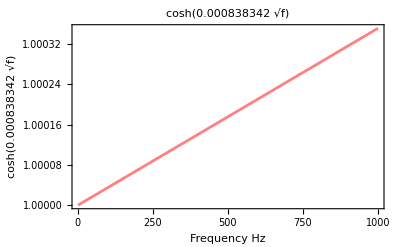

```mathematica
cosh=Cosh[ξ]/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
coshg=Plot[cosh,{f,1,1000},PlotLabel->cosh,PlotStyle->{Pink}, Frame->True,FrameLabel->{Frequency(Hz),cosh}]
```

sinh[ξ]

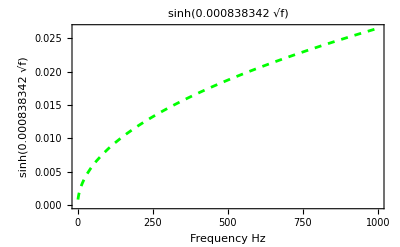

```mathematica
sinh=Sinh[ξ]/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
sinhg=Plot[sinh,{f,1,1000},PlotLabel->sinh,PlotStyle->{Dashed,Green}, Frame->True,FrameLabel->{Frequency(Hz),sinh}]
```

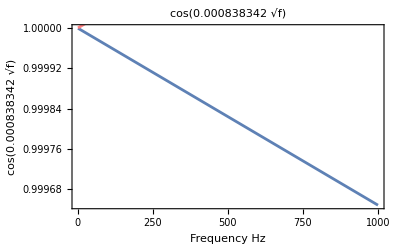

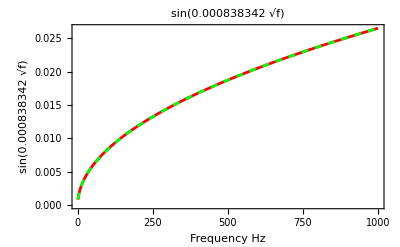

```mathematica
Show[cosg,coshg]
Show[sing,sinhg]
```